```mathematica
Quit[];
```

## Run This First

```mathematica
SetDirectory@NotebookDirectory[]
PacletDirectoryLoad["."]
<<DionicKNGeodesics`
```

/Users/conordyson/Desktop/GenericDionicKerrNewmannGeodesics

{/Users/conordyson/Desktop/GenericDionicKerrNewmannGeodesics}

This Package builds upon the Black Hole Perturbation ToolKit using our new solutions for Dionic Geodesics in terms of Jacobi elliptic functions

This Package takes M = 1 and  m=1, with the latter having the action of rescaling e and g which appearing within Ω and δ. All additional quantities are defined as found in  - add arxiv number.

The Keys associated with the output functions are 
“a” -> a,
“Parametrization”->”Mino”, 
“ChargeParameters”->{𝒪 , Ω, δ},
“Energy” -> ℰ, 
“AngularMomentum” -> ℒ, 
“CarterConstant” -> 𝒦, 
“ConstantsOfMotion” -> consts,
“Periods”-> <|2π/Υr, 2π/Υθ|>(only works for plunging with complex roots),
“RadialRoots”-> {R1,R2,R3,R4},
“PolarRoots”-> {z1,z2,z3,z3},
“EllipticBasis” ->  <| kr, kz|>,
“RadialRootCrossingTimeMino”-> <| Abs[MinoR[R1]] - MinoR[r0](* Time outgoing to inner root*), Abs[MinoR[R2]] - MinoR[r0](* Time outgoing to outer root*)|>,
“Trajectory” -> {t,r,θ,ϕ}

# Orbits in KerrNewmann Spacetime for Dionic motion

## Generic Plunges

```mathematica
a = 0.9;
𝒪 = 0.2;
Ω  = 10.2;
δ = -0.2;
ℰ = 0.96;
ℒ = 0.4;
𝒦 = 10.4;
RP = 1+Sqrt[1-a^2-𝒪^2];
RM = 1-Sqrt[1-a^2-𝒪^2];
orbit = DionicKNGeoPlunge[a,𝒪 ,Ω,δ,ℰ ,ℒ ,𝒦];
{t,r,θ,ϕ} = orbit["Trajectory"];
{ℰ, 𝒪, Ω,ℒ,𝒦} = {"ℰ",  "𝒪", "Ω","ℒ" ,"𝒦"}/.orbit["ConstantsOfMotion"];
z[λ_]:= Cos[θ[λ]];
```

```mathematica
path[λ_]:= {Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}
P1 = ParametricPlot3D[path[λ],{λ,-100,-90}, MaxRecursion->10, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

## Generic Orbits

```mathematica
a = 0.4;
𝒪 = 0.5;
Ω  = -5.2;
ℰ = 0.974;
δ=-0.3;
ℒ = 4.2;
𝒦 = 2.2;
RP = 1+Sqrt[1-a^2-𝒪^2];
RM = 1-Sqrt[1-a^2-𝒪^2];
orbit =DionicKNGeoOrbit[a,𝒪 ,Ω,δ,ℰ ,ℒ ,𝒦];
{t,r,θ,ϕ} = orbit["Trajectory"];
{ℰ, 𝒪, Ω,δ,ℒ,𝒦} = {"ℰ",  "𝒪", "Ω","δ","ℒ" ,"𝒦"}/.orbit["ConstantsOfMotion"];
z[λ_]:= Cos[θ[λ]];
```

```mathematica
path[λ_]:= {Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}

P1 = ParametricPlot3D[path[λ],{λ,-10,0}, MaxRecursion->10, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

## Testing Solutions - By Plugging back Into Equations of Motion

### Radial

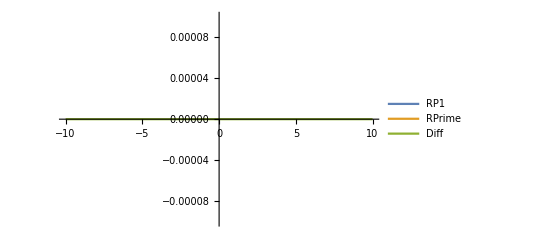

```mathematica
RPoly1[r_]:= (ℰ(r^2+a^2)-a*ℒ- δ r )^2-(r^2-2*r+a^2+𝒪^2)(r^2+(a*ℰ-ℒ)^2+𝒦)

Plot[{RPoly1[r[λ]], (r'[λ])^2, (r'[λ])^2- RPoly1[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange-> {{-10,10},{-0.0001,0.0001}}]
```

### Polar

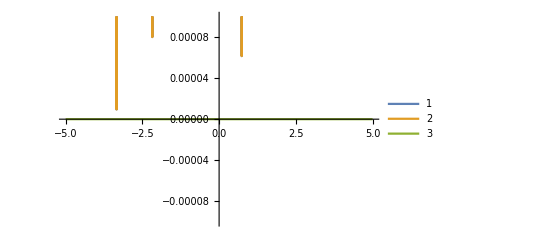

```mathematica
z[λ_] := Cos[θ[λ]]
Polyθ[z_] :=𝒦-z^2 𝒦-z(Ω^2 z+2 a  Ω (-1+z^2) ℰ+a^2  z (-1+z^2) (-1+ℰ^2)+2  Ω ℒ+ z ℒ^2);
Plot[{(z'[λ])^2, Polyθ[z[λ] ], (z'[λ])^2- Polyθ[z[λ] ]}, {λ,-5,5}, PlotLegends->Automatic , PlotRange-> {{-5,5}, {-0.0001,0.0001}},PlotLegends->{PolyθQ,θQ,θQ-PolyθQ}]
```

### Azimuthal

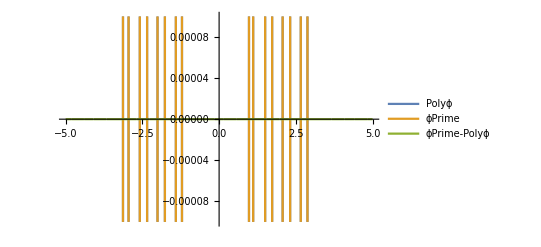

```mathematica
Polyϕ[λ_]:= (Ω z[λ]+ (ℒ-a (1-z[λ]^2) ℰ))/(1-z[λ]^2)-a/((r[λ]-RP)(r[λ]-RM)) (δ r[λ] + a ℒ - (a^2+r[λ]^2)ℰ)
Plot[{Re[Polyϕ[λ]],ϕ'[λ],ϕ'[λ]-Polyϕ[λ]},{λ,-5,5},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}, PlotRange->{{-5,5}, {-0.0001,0.0001}}]
```

### Time

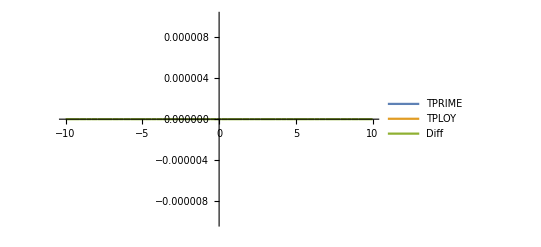

```mathematica
TPoly[λ_]:=  ((a^2+r[λ]^2) ( (a^2+r[λ]^2) ℰ-a ℒ - r[λ]δ))/((r[λ]-RP)(r[λ]-RM))+ a(Ω z[λ]-a (1-z[λ]^2) ℰ+ℒ) 
Plot[{TPoly[λ],t'[λ], TPoly[λ]- t'[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}, PlotRange->{{-10,10},{-0.000010,0.000010}}]
```

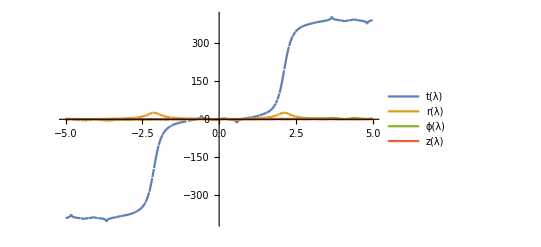

```mathematica
Plot[{t[λ], r[λ],ϕ[λ],z[λ]},{λ,-5,5},PlotLegends->"Expressions", PlotRange->All]
```